```mathematica
SqExp[ℓ_][a_,b_]:=Exp[-EuclideanDistance[a,b]^2/(2ℓ)]
OrnsteinUhlenbeck[ℓ_][a_,b_]:=Exp[-EuclideanDistance[a,b]/ℓ]
Matern[ν_][ℓ_][a_,b_]:=With[{r=EuclideanDistance[a,b]},
2^(1-ν)/Gamma[ν]((√(2ν)r)/ℓ)^ν BesselK[ν,(√(2ν)r)/ℓ]]

SqExpC[ℓ_]:=Compile[{{a,_Real},{b,_Real}},Exp[-Abs[a-b]^2/(2 ℓ^2)]]
OrnsteinUhlenbeckC[ℓ_]:=Compile[{{a,_Real},{b,_Real}},Exp[-Abs[a-b]/ℓ]]

Block[{ℓ,a,b},
Matern[3/2][ℓ_][a_,b_]:=Evaluate[Matern[3/2][ℓ][a,b]//FullSimplify];
Matern[5/2][ℓ_][a_,b_]:=Evaluate[Matern[5/2][ℓ][a,b]//FullSimplify];
Matern[7/2][ℓ_][a_,b_]:=Evaluate[Matern[7/2][ℓ][a,b]//FullSimplify]]
```

```mathematica
Krig[Kernel_,X_,Y_]:=Krig[Kernel,X,Y,0]

Krig[Kernel_,X_,Y_,v_]:=
With[{Σ22=Outer[Kernel,X,X]+v IdentityMatrix[Length[X]]},
With[{Σ22i=LinearSolve[Σ22]},
Compile[{{p,_Real}},
Module[{μ,σ2,Σ,Σ11,Σ12,Σ21},
Σ11=Outer[Kernel,{p},{p}];
Σ12=Outer[Kernel,{p},X];
Σ21=Transpose[Σ12];
μ=Dot[Σ12,Σ22i[Y]]//First;
Σ=Σ11-Dot[Σ12,Σ22i[Σ21]];
σ2=Σ⟦1,1⟧;
{μ,σ2}],
RuntimeOptions->{
"EvaluateSymbolically"->False},
CompilationOptions->{
"ExpressionOptimization"->True,
"InlineExternalDefinitions"->True,
"InlineCompiledFunctions"->True}]]]
```

```mathematica
GPMIGainC=
Compile[{{μ,_Real},{σ,_Real},{α,_Real},{γ,_Real}},
√α(√(σ^2+γ)-√γ),
CompilationOptions->{"ExpressionOptimization" -> False},
RuntimeOptions->{"EvaluateSymbolically"->False}]
```

CompiledFunction[…]

```mathematica
GPMIPlot[Kernel_,X_,Y_,α_,γ_]:=
With[{f=Krig[Kernel,X,Y]},
Block[{μ,σ,σ2,plotf},
plotf[body_]:=With[{module=Module},
Function[{x},module[{μ,σ,σ2},{μ,σ2}=f[x];σ=√σ2;body]]];

With[{
mean=plotf[μ],
low=plotf[μ-σ],
high=plotf[μ+σ],
gain=plotf[μ+GPMIGainC[μ,σ,α,γ]]
},
Plot[{mean[x],low[x],high[x],gain[x]},{x,0,1},
PlotRange->{-1.1,1.5},
PlotStyle->{Dashed,None,None,Automatic,Automatic},
Filling->{2->{3}}]
]]]
```

```mathematica
Manipulate[
Module[{X,Y,t},
{X,Y}=Transpose[p];
t=Max[Y];
GPMIPlot[Kernel[ℓ],X,Y,Log[2/δ],γ]],
{{p,{{1/2,0},{1/4,1/4},{9/10,1/10}}},
{0,-1},{1,1.5},Locator},
{Kernel,{SqExpC,OrnsteinUhlenbeckC,Matern[3/2],Matern[5/2]}},
{{ℓ,0.2},0.01,0.4},
{{δ,0.1},0.001,1},
{{γ,0.5},0,5},
SaveDefinitions->True]
```

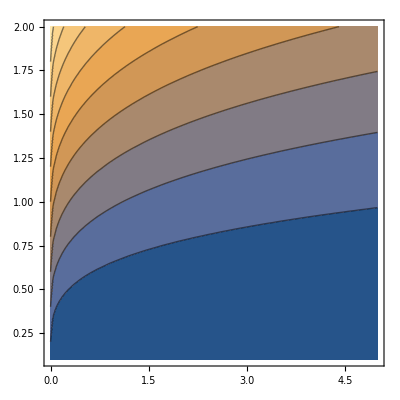

```mathematica
ContourPlot[(√(σ^2+γ)-√γ),{γ,0,5},{σ,0.1,2}]
```